```mathematica
Clear[a,b,c,n,m,x,r,a,G,phi]
rho:=1
theta0:=π/3
f[θ_]:=5 θ ⅇ^(-2 θ)
nTerms:=10
lambda[n_]:=((π n)/theta0)^2
phi[θ_,n_]:=Sin[θ √lambda[n]]
G[r_,n_]:=r^(√lambda[n])
B[n_]:=(2 ∫_0^theta0 f[θ] phi[θ,n]ⅆθ)/(theta0 G[rho,n])
u[r_,θ_,M_]:=∑_(n=1)^M B[n] G[r,n] phi[θ,n]
z[r_,θ_]:=Evaluate[u[r,θ,nTerms]]
ParametricPlot3D[{r*Cos[θ],r*Sin[θ],z[r,θ]},{r,0,rho},{θ,0,theta0}]
```

-Graphics3D-

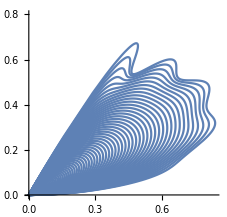

```mathematica
myPlots:=Table[PolarPlot[z[r,θ],{θ,0,theta0},PlotRange->{0,0.8}],{r,0,rho,.01}]

Show[myPlots]
```